```mathematica
x00t=(k*xtot0*f000*Exp[(r-2*μ)*t])/(k+xtot0*(Exp[r*t]-1));
x1t=(k*xtot0*Exp[(r-2*μ)*t]*(-2*f000+Exp[t*μ]*(f000+1)))/(k+xtot0*(Exp[r*t]-1));
x11t=(k*xtot0*Exp[(r-2*μ)*t]*(Exp[t*μ]-1)*(-f000+Exp[t*μ]))/(k+xtot0*(Exp[r*t]-1));
x00tM=x00t/.t->tM;
x1tM=x1t/.t->tM;
x11tM=x11t/.t->tM;
x00T=x00tM+0.5*x1tM-1/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
x1T=2/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
x11T=x11tM+0.5*x1tM-1/((0.5*x1tM)^-1+α*Pr*(t-tM))//FullSimplify;
changef000=x00T/(x00T+x1T)-f000//FullSimplify;
Numerator[Together[changef000]]//FullSimplify;
Solve[%==0,f000];
f000/.%;
f000=%13[[3]];
params={r->2,k->1,t->25,α->0.3,Pr->0.1,xtot0->0.05};
xhealthy=(ⅇ^(tM (r-μ)) (0.5+0.5 f000) k xtot0)/(k+(-1.+ⅇ^(r tM)) xtot0)+1/((2. ⅇ^(-tM (r-2 μ)) (k+(-1+ⅇ^(r tM)) xtot0))/((-2 f000+ⅇ^(tM μ) (1+f000)) k xtot0)+Pr (t-tM) α)/.params;
dx00x1dtM=D[xhealthy,tM];
f[mu_]:=FindRoot[Re[dx00x1dtM/.params/.μ->mu]==0,{tM,3}]
```

```mathematica
Table[f[i],{i,0.002,0.2,0.002}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{tM→4.9256},{tM→4.57852},{tM→4.37529},{tM→4.23095},{tM→4.11887},{tM→4.02721},{tM→3.94963},{tM→3.88236},{tM→3.82296},{tM→3.76978},{tM→3.72162},{tM→3.67761},{tM→3.63708},{tM→3.59952},{tM→3.56452},{tM→3.53174},{tM→3.50092},{tM→3.47183},{tM→3.44429},{tM→3.41813},{tM→3.39322},{tM→3.36945},{tM→3.34672},{tM→3.32492},{tM→3.304},{tM→3.28388},{tM→3.26449},{tM→3.2458},{tM→3.22773},{tM→3.21027},{tM→3.19336},{tM→3.17697},{tM→3.16106},{tM→3.14562},{tM→3.13061},{tM→3.11601},{tM→3.10179},{tM→3.08793},{tM→3.07443},{tM→3.06125},{tM→3.04838},{tM→3.03581},{tM→3.02352},{tM→3.0115},{tM→2.99974},{tM→2.98823},{tM→2.97695},{tM→2.9659},{tM→2.95507},{tM→2.94444},{tM→2.93401},{tM→2.92377},{tM→2.91372},{tM→2.90385},{tM→2.89415},{tM→2.88461},{tM→2.87523},{tM→2.866},{tM→2.85692},{tM→2.84799},{tM→2.83919},{tM→2.83053},{tM→2.82199},{tM→2.81359},{tM→2.8053},{tM→2.79713},{tM→2.78908},{tM→2.78113},{tM→2.7733},{tM→2.76556},{tM→2.75793},{tM→2.7504},{tM→2.74297},{tM→2.73562},{tM→2.72837},{tM→2.72121},{tM→2.71413},{tM→2.70714},{tM→2.70023},{tM→2.69339},{tM→2.68664},{tM→2.67996},{tM→2.67335},{tM→2.66682},{tM→2.66036},{tM→2.65396},{tM→2.64763},{tM→2.64137},{tM→2.63517},{tM→2.62904},{tM→2.62296},{tM→2.61695},{tM→2.61099},{tM→2.60509},{tM→2.59925},{tM→2.59346},{tM→2.58773},{tM→2.58204},{tM→2.57641},{tM→2.57083}}

```mathematica
Table[%[[i,1,2]],{i,1,Length[%]}];
```

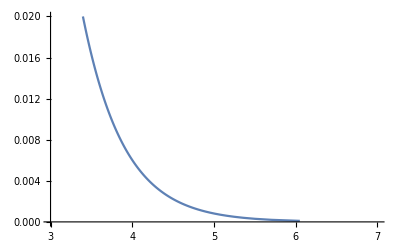

```mathematica
ListLinePlot[Transpose[{%20,0.0001*Range[200]}],PlotRange->{{3,7},{0,0.02}}]
```